```mathematica
(*1.1 ratio of 137174210,1111111111 *)

N[137174210.0/1111111111,50]
N[137174210/1111111111,50]
```

0.123457

0.1234567890123456789012345678901234567890123456789

```mathematica
(* 1.2 value of i^-i and e^(-π/2)*)

N[ⅈ^ⅈ]
N[ⅇ^(-π/2)]
N[ⅈ^ⅈ]-N[ⅇ^(-π/2)]
```

0.20788+0. ⅈ

0.20788

0.+0. ⅈ

```mathematica
(* 1.3 factorial*)

100!
300!
500!
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000

306057512216440636035370461297268629388588804173576999416776741259476533176716867465515291422477573349939147888701726368864263907759003154226842927906974559841225476930271954604008012215776252176854255965356903506788725264321896264299365204576448830388909753943489625436053225980776521270822437639449120128678675368305712293681943649956460498166450227716500185176546469340112226034729724066333258583506870150169794168850353752137554910289126407157154830282284937952636580145235233156936482233436799254594095276820608062232812387383880817049600000000000000000000000000000000000000000000000000000000000000000000000000

1220136825991110068701238785423046926253574342803192842192413588385845373153881997605496447502203281863013616477148203584163378722078177200480785205159329285477907571939330603772960859086270429174547882424912726344305670173270769461062802310452644218878789465754777149863494367781037644274033827365397471386477878495438489595537537990423241061271326984327745715546309977202781014561081188373709531016356324432987029563896628911658974769572087926928871281780070265174507768410719624390394322536422605234945850129918571501248706961568141625359056693423813008856249246891564126775654481886506593847951775360894005745238940335798476363944905313062323749066445048824665075946735862074637925184200459369692981022263971952597190945217823331756934581508552332820762820023402626907898342451712006207714640979456116127629145951237229913340169552363850942885592018727433795173014586357570828355780158735432768888680120399882384702151467605445407663535984174430480128938313896881639487469658817504506926365338175055478128640000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
4.5!
3.2!
```

52.3428

7.75669

```mathematica
(* 1.4 factor x^10-1 *)

Factor[x^10-1]
```

(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)

```mathematica
Expand[(-1+x) (1+x) (1-x+x^2-x^3+x^4) (1+x+x^2+x^3+x^4)]
```

-1+x^10

```mathematica
(* 1.5 find prime factors using FactorInterger *)

FactorInteger[9699690]
FactorInteger[9765625]
```

{{2,1},{3,1},{5,1},{7,1},{11,1},{13,1},{17,1},{19,1}}

{{5,10}}

```mathematica
(* 1.6 evaluate (a+b)^100 *)

Expand[(a+b)^100]
```

a^100+100 a^99 b+4950 a^98 b^2+161700 a^97 b^3+3921225 a^96 b^4+75287520 a^95 b^5+1192052400 a^94 b^6+16007560800 a^93 b^7+186087894300 a^92 b^8+1902231808400 a^91 b^9+17310309456440 a^90 b^10+141629804643600 a^89 b^11+1050421051106700 a^88 b^12+7110542499799200 a^87 b^13+44186942677323600 a^86 b^14+253338471349988640 a^85 b^15+1345860629046814650 a^84 b^16+6650134872937201800 a^83 b^17+30664510802988208300 a^82 b^18+132341572939212267400 a^81 b^19+535983370403809682970 a^80 b^20+2041841411062132125600 a^79 b^21+7332066885177656269200 a^78 b^22+24865270306254660391200 a^77 b^23+79776075565900368755100 a^76 b^24+242519269720337121015504 a^75 b^25+699574816500972464467800 a^74 b^26+1917353200780443050763600 a^73 b^27+4998813702034726525205100 a^72 b^28+12410847811948286545336800 a^71 b^29+29372339821610944823963760 a^70 b^30+66324638306863423796047200 a^69 b^31+143012501349174257560226775 a^68 b^32+294692427022540894366527900 a^67 b^33+580717429720889409486981450 a^66 b^34+1095067153187962886461165020 a^65 b^35+1977204582144932989443770175 a^64 b^36+3420029547493938143902737600 a^63 b^37+5670048986634686922786117600 a^62 b^38+9013924030034630492634340800 a^61 b^39+13746234145802811501267369720 a^60 b^40+20116440213369968050635175200 a^59 b^41+28258808871162574166368460400 a^58 b^42+38116532895986727945334202400 a^57 b^43+49378235797073715747364762200 a^56 b^44+61448471214136179596720592960 a^55 b^45+73470998190814997343905056800 a^54 b^46+84413487283064039501507937600 a^53 b^47+93206558875049876949581681100 a^52 b^48+98913082887808032681188722800 a^51 b^49+100891344545564193334812497256 a^50 b^50+98913082887808032681188722800 a^49 b^51+93206558875049876949581681100 a^48 b^52+84413487283064039501507937600 a^47 b^53+73470998190814997343905056800 a^46 b^54+61448471214136179596720592960 a^45 b^55+49378235797073715747364762200 a^44 b^56+38116532895986727945334202400 a^43 b^57+28258808871162574166368460400 a^42 b^58+20116440213369968050635175200 a^41 b^59+13746234145802811501267369720 a^40 b^60+9013924030034630492634340800 a^39 b^61+5670048986634686922786117600 a^38 b^62+3420029547493938143902737600 a^37 b^63+1977204582144932989443770175 a^36 b^64+1095067153187962886461165020 a^35 b^65+580717429720889409486981450 a^34 b^66+294692427022540894366527900 a^33 b^67+143012501349174257560226775 a^32 b^68+66324638306863423796047200 a^31 b^69+29372339821610944823963760 a^30 b^70+12410847811948286545336800 a^29 b^71+4998813702034726525205100 a^28 b^72+1917353200780443050763600 a^27 b^73+699574816500972464467800 a^26 b^74+242519269720337121015504 a^25 b^75+79776075565900368755100 a^24 b^76+24865270306254660391200 a^23 b^77+7332066885177656269200 a^22 b^78+2041841411062132125600 a^21 b^79+535983370403809682970 a^20 b^80+132341572939212267400 a^19 b^81+30664510802988208300 a^18 b^82+6650134872937201800 a^17 b^83+1345860629046814650 a^16 b^84+253338471349988640 a^15 b^85+44186942677323600 a^14 b^86+7110542499799200 a^13 b^87+1050421051106700 a^12 b^88+141629804643600 a^11 b^89+17310309456440 a^10 b^90+1902231808400 a^9 b^91+186087894300 a^8 b^92+16007560800 a^7 b^93+1192052400 a^6 b^94+75287520 a^5 b^95+3921225 a^4 b^96+161700 a^3 b^97+4950 a^2 b^98+100 a b^99+b^100

```mathematica
Coefficient[Expand[(a+b)^100],a^50 b^50]
```

100891344545564193334812497256

```mathematica
(* 1.7 substitute and reduce *)

x^4+y^4 /.x->Cos[z]/.y->Sin[z]
```

Cos[z]^4+Sin[z]^4

```mathematica
TrigReduce[x^4+y^4 /.x->Cos[z]/.y->Sin[z]]
TrigExpand[x^4+y^4 /.x->Cos[z]/.y->Sin[z]]
TrigToExp[x^4+y^4 /.x->Cos[z]/.y->Sin[z]]
```

1/4 (3+Cos[4 z])

3/4+Cos[z]^4/4-3/2 Cos[z]^2 Sin[z]^2+Sin[z]^4/4

3/4+1/8 ⅇ^(-4 ⅈ z)+1/8 ⅇ^(4 ⅈ z)

```mathematica
(* 1.8 indefinite integral *)

∫1/(1+x^2)ⅆx
TableForm[Table[∫1/(1+x^a)ⅆx,{a,1,10,1}]]
```

ArcTan[x]

Log[1+x]
ArcTan[x]
ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]
(-2 ArcTan[1-√2 x]+2 ArcTan[1+√2 x]-Log[1-√2 x+x^2]+Log[1+√2 x+x^2])/(4 √2)
1/20 (-2 √(10-2 √5) ArcTan[(1+√5-4 x)/(√(10-2 √5))]+2 √(2 (5+√5)) ArcTan[(-1+√5+4 x)/(√(2 (5+√5)))]+4 Log[1+x]+(-1+√5) Log[1+1/2 (-1+√5) x+x^2]-(1+√5) Log[1-1/2 (1+√5) x+x^2])
1/12 (-2 ArcTan[√3-2 x]+4 ArcTan[x]+2 ArcTan[√3+2 x]-√3 Log[1-√3 x+x^2]+√3 Log[1+√3 x+x^2])
2/7 ArcTan[Sec[π/14] (x-Sin[π/14])] Cos[π/14]+2/7 ArcTan[Sec[(3 π)/14] (x+Sin[(3 π)/14])] Cos[(3 π)/14]+1/7 Log[1+x]-1/7 Cos[π/7] Log[1+x^2-2 x Cos[π/7]]-1/7 Log[1+x^2-2 x Sin[π/14]] Sin[π/14]+2/7 ArcTan[(x-Cos[π/7]) Csc[π/7]] Sin[π/7]+1/7 Log[1+x^2+2 x Sin[(3 π)/14]] Sin[(3 π)/14]
1/4 ArcTan[Sec[π/8] (x-Sin[π/8])] Cos[π/8]+1/4 ArcTan[Sec[π/8] (x+Sin[π/8])] Cos[π/8]-1/8 Cos[π/8] Log[1+x^2-2 x Cos[π/8]]+1/8 Cos[π/8] Log[1+x^2+2 x Cos[π/8]]+1/4 ArcTan[(x-Cos[π/8]) Csc[π/8]] Sin[π/8]+1/4 ArcTan[(x+Cos[π/8]) Csc[π/8]] Sin[π/8]-1/8 Log[1+x^2-2 x Sin[π/8]] Sin[π/8]+1/8 Log[1+x^2+2 x Sin[π/8]] Sin[π/8]
1/18 (2 √3 ArcTan[(-1+2 x)/(√3)]+4 ArcTan[Sec[π/18] (x+Sin[π/18])] Cos[π/18]+2 Log[1+x]-Log[1-x+x^2]-2 Cos[π/9] Log[1+x^2-2 x Cos[π/9]]+2 Cos[(2 π)/9] Log[1+x^2+2 x Cos[(2 π)/9]]+2 Log[1+x^2+2 x Sin[π/18]] Sin[π/18]-4 ArcTan[Cot[π/9]-x Csc[π/9]] Sin[π/9]+4 ArcTan[(x+Cos[(2 π)/9]) Csc[(2 π)/9]] Sin[(2 π)/9])
1/40 (2 (-1+√5) ArcTan[(√(2 (5+√5))-4 x)/(1-√5)]+8 ArcTan[x]+2 (1+√5) ArcTan[(-√(10-2 √5)+4 x)/(1+√5)]+2 (1+√5) ArcTan[(√(10-2 √5)+4 x)/(1+√5)]+2 (-1+√5) ArcTan[(√(2 (5+√5))+4 x)/(-1+√5)]-√(10-2 √5) Log[1-√(1/2 (5-√5)) x+x^2]+√(10-2 √5) Log[1+√(1/2 (5-√5)) x+x^2]-√(2 (5+√5)) Log[1-√(1/2 (5+√5)) x+x^2]+√(2 (5+√5)) Log[1+√(1/2 (5+√5)) x+x^2])

```mathematica
(* 1.9 indefinite integral *)

∫1/Sin[x] ⅆx
```

-Log[Cos[x/2]]+Log[Sin[x/2]]

```mathematica
TrigReduce[
D[-Log[Cos[x/2]]+Log[Sin[x/2]],x]
]
Simplify[
D[-Log[Cos[x/2]]+Log[Sin[x/2]],x]
]
```

1/2 Csc[x/2] Sec[x/2]

Csc[x]

```mathematica
TrigReduce[D[(-Log[Cos[x/2]]+Log[Sin[x/2]]), x]]
```

1/2 Csc[x/2] Sec[x/2]

```mathematica
(* 1.10 *)

g[x_]:= ∫_x^(x^3) Sin[x t^2]ⅆt
```

```mathematica
D[g[x],x]
```

-(√(π/2) (-FresnelS[√(2/π) x^(3/2)]+FresnelS[√(2/π) x^(7/2)]))/(2 x^(3/2))+(√(π/2) (-(3 √x Sin[x^3])/(√(2 π))+(7 x^(5/2) Sin[x^7])/(√(2 π))))/(√x)

```mathematica
g'[3]
```

-1/6 √(π/6) (-FresnelS[3 √(6/π)]+FresnelS[27 √(6/π)])+√(π/6) (-3 √(3/(2 π)) Sin[27]+63 √(3/(2 π)) Sin[2187])

```mathematica
(* 1.11 *)
(* g[x_]:=∫_Sin[x]^Cos[x] ⅇ^(x^2 t^3)ⅆt  *)
```

```mathematica
(* find roots of the polynomials *)

Solve[x^3-3 x^2+5x-2==0,x]
N[Solve[x^3-3 x^2+5x-2==0,x]]
FindRoot[x^3-3 x^2+5x-2,{x,0}]
```

{{x→1-2 (2/(3 (-9+√177)))^(1/3)+(1/2 (-9+√177))^(1/3)/3^(2/3)},{x→1+(1+ⅈ √3) (2/(3 (-9+√177)))^(1/3)-((1-ⅈ √3) (1/2 (-9+√177))^(1/3))/(2 3^(2/3))},{x→1+(1-ⅈ √3) (2/(3 (-9+√177)))^(1/3)-((1+ⅈ √3) (1/2 (-9+√177))^(1/3))/(2 3^(2/3))}}

{{x→0.546602},{x→1.2267+1.46771 ⅈ},{x→1.2267-1.46771 ⅈ}}

{x→0.546602}

```mathematica
Solve[3 x^3-2 x^2+7x-9==0,x]
N[Solve[3 x^3-2 x^2+7x-9==0,x]]
FindRoot[3 x^3-2 x^2+7x-9,{x,0}]
```

{{x→1/9 (2-59 (2/(1825+9 √51261))^(1/3)+(1/2 (1825+9 √51261))^(1/3))},{x→2/9-1/18 (1+ⅈ √3) (1/2 (1825+9 √51261))^(1/3)+(59 (1-ⅈ √3))/(9 2^(2/3) (1825+9 √51261)^(1/3))},{x→2/9-1/18 (1-ⅈ √3) (1/2 (1825+9 √51261))^(1/3)+(59 (1+ⅈ √3))/(9 2^(2/3) (1825+9 √51261)^(1/3))}}

{{x→1.07952},{x→-0.206426-1.65421 ⅈ},{x→-0.206426+1.65421 ⅈ}}

{x→1.07952}

```mathematica
Solve[x^5-x^4+5 x^3-7 x^2-3x+13==0,x]
N[Solve[x^5-x^4+5 x^3-7 x^2-3x+13==0,x]]
FindRoot[x^5-x^4+5 x^3-7 x^2-3x+13==0,{x,0}]
```

{{x→Root[13-3 #1-7 #1^2+5 #1^3-#1^4+#1^5&,1]},{x→Root[13-3 #1-7 #1^2+5 #1^3-#1^4+#1^5&,2]},{x→Root[13-3 #1-7 #1^2+5 #1^3-#1^4+#1^5&,3]},{x→Root[13-3 #1-7 #1^2+5 #1^3-#1^4+#1^5&,4]},{x→Root[13-3 #1-7 #1^2+5 #1^3-#1^4+#1^5&,5]}}

{{x→-1.0539},{x→-0.209807-2.48497 ⅈ},{x→-0.209807+2.48497 ⅈ},{x→1.23676-0.673685 ⅈ},{x→1.23676+0.673685 ⅈ}}

{x→-1.0539}

```mathematica
(* 1.13 *)

Solve[ⅇ^x-Tan[x]==0,x]
```

Solve[ⅇ^x-Tan[x]==0,x]

```mathematica
(* 1.20 *)

g[x_]=∫_0^(π/2) √(1-x^2 Sin[t]^2)ⅆt
```

ConditionalExpression[EllipticE[x^2],Re[x^2]≤1||x^2∉ℝ]

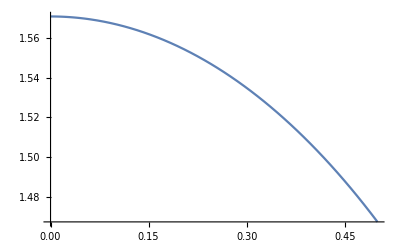

```mathematica
Plot[g[x],{x,0,0.5}]
```

```mathematica
(* 1.21 *)

g[x_,y_]=∫_0^y Sin[x t^2]ⅆt
```

(√(π/2) FresnelS[√(2/π) √x y])/(√x)

```mathematica
Plot3D[g[x,y],{x,0,2},{y,0,2π}]
```

-Graphics3D-

```mathematica
(* 1.25 *)

Re[5/((1-I)(2-I)(3-I))]
Im[5/((1-I)(2-I)(3-I))]
```

0

1/2

```mathematica
Re[(1+2I)/(3-4I)+(2-I)/(5I)]
Im[(1+2I)/(3-4I)+(2-I)/(5I)]
```

-2/5

0

```mathematica
Simplify[Re[(a-I b)(2a+2I b)]]
Simplify[Im[(a-I b)(2a+2I b)]]
```

2 Re[a^2+b^2]

2 Im[a^2+b^2]

```mathematica
Re[(2-3I)(1+I)]
Im[(2-3I)(1+I)]
```

5

-1

```mathematica
(* 1.26 convert to polar form *)
```

```mathematica
Abs[2-ⅈ]Arg[2-ⅈ]
```

-√5 ArcTan[1/2]

```mathematica
Abs[ⅈ/(1+ⅈ)]Arg[ⅈ/(1+ⅈ)]
```

π/(4 √2)

```mathematica
(* 1.27 find real and imaginary parts *)
```

```mathematica
Re[(1+ⅈ √3)^3]
Im[(1+ⅈ √3)^3]
```

-8

0

```mathematica
Re[(2+ⅈ)^53]
Im[(2+ⅈ)^53]
```

2824084520626955002

-1768269455316917239

```mathematica
Re[((1+ⅈ √3)/(√3+ⅈ))^217]
Im[((1+ⅈ √3)/(√3+ⅈ))^217]
```

(√3)/2

1/2

```mathematica
(* Spherical Harmonics *)
```

```mathematica
Subscript[Y, 21][θ_,ϕ_] := -√(15/(8π))ⅇ^(ⅈ ϕ)Sin[θ]Cos[θ];
Subscript[Y, 22][θ_,ϕ_] := -√(15/(32π))ⅇ^(2ⅈ ϕ)Sin[θ]^2;
x1=Re[Subscript[Y, 21][θ,ϕ]]Sin[θ]Cos[ϕ];
y1=Re[Subscript[Y, 21][θ,ϕ]]Sin[θ]Sin[ϕ];
z1=Re[Subscript[Y, 21][θ,ϕ]]Cos[θ];

x2=Abs[Subscript[Y, 21][θ,ϕ]]Sin[θ]Cos[ϕ];
y2=Abs[Subscript[Y, 21][θ,ϕ]]Sin[θ]Sin[ϕ];
z2=Abs[Subscript[Y, 21][θ,ϕ]]Cos[θ];

a1=Re[Subscript[Y, 22][θ,ϕ]]Sin[θ]Cos[ϕ];
b1=Re[Subscript[Y, 22][θ,ϕ]]Sin[θ]Sin[ϕ];
c1=Re[Subscript[Y, 22][θ,ϕ]]Cos[θ];

a2=Abs[Subscript[Y, 22][θ,ϕ]]Sin[θ]Cos[ϕ];
b2=Abs[Subscript[Y, 22][θ,ϕ]]Sin[θ]Sin[ϕ];
c2=Abs[Subscript[Y, 22][θ,ϕ]]Cos[θ];

ParametricPlot3D[
{x1,y1,z1},
{θ,0,2π},{ϕ,0,π}
]
ParametricPlot3D[
{x2,y2,z2},
{θ,0,2π},{ϕ,0,π}
]
ParametricPlot3D[
{a1,b1,c1},
{θ,0,2π},{ϕ,0,π}
]
ParametricPlot3D[
{a2,b2,c2},
{θ,0,2π},{ϕ,0,π}
]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
r= Abs[SphericalHarmonicY[2,2,θ,ϕ]];
x=r Sin[θ]Cos[ϕ];
y=r Sin[θ]Sin[ϕ];
z=r Cos[θ];
```

```mathematica
ParametricPlot3D[
{x,y,z},
{θ,0,2π},{ϕ,0,π}
]
```

-Graphics3D-